```mathematica
ClearAll["Global`*"]
(* set your home directory *)
SetDirectory[NotebookDirectory[]];
```

# Draw Mesh

```mathematica
nodes=Import["nodes.dat"];
ribs=Import["ribs.dat"];
triangles=Import["triangles.dat"]+1;
```

```mathematica
Do[
Subscript[𝒯, i]=MeshRegion[nodes,{
Labeled[Line@{triangles[[i,2]],triangles[[i,3]]},ribs[[i,1]]],
Labeled[Line@{triangles[[i,3]],triangles[[i,1]]},ribs[[i,2]]],
Labeled[Line@{triangles[[i,1]],triangles[[i,2]]},ribs[[i,3]]]
}],
{i,Length@triangles}]
```

```mathematica
𝒯=Table[Subscript[𝒯, i],{i,Length@triangles}];
```

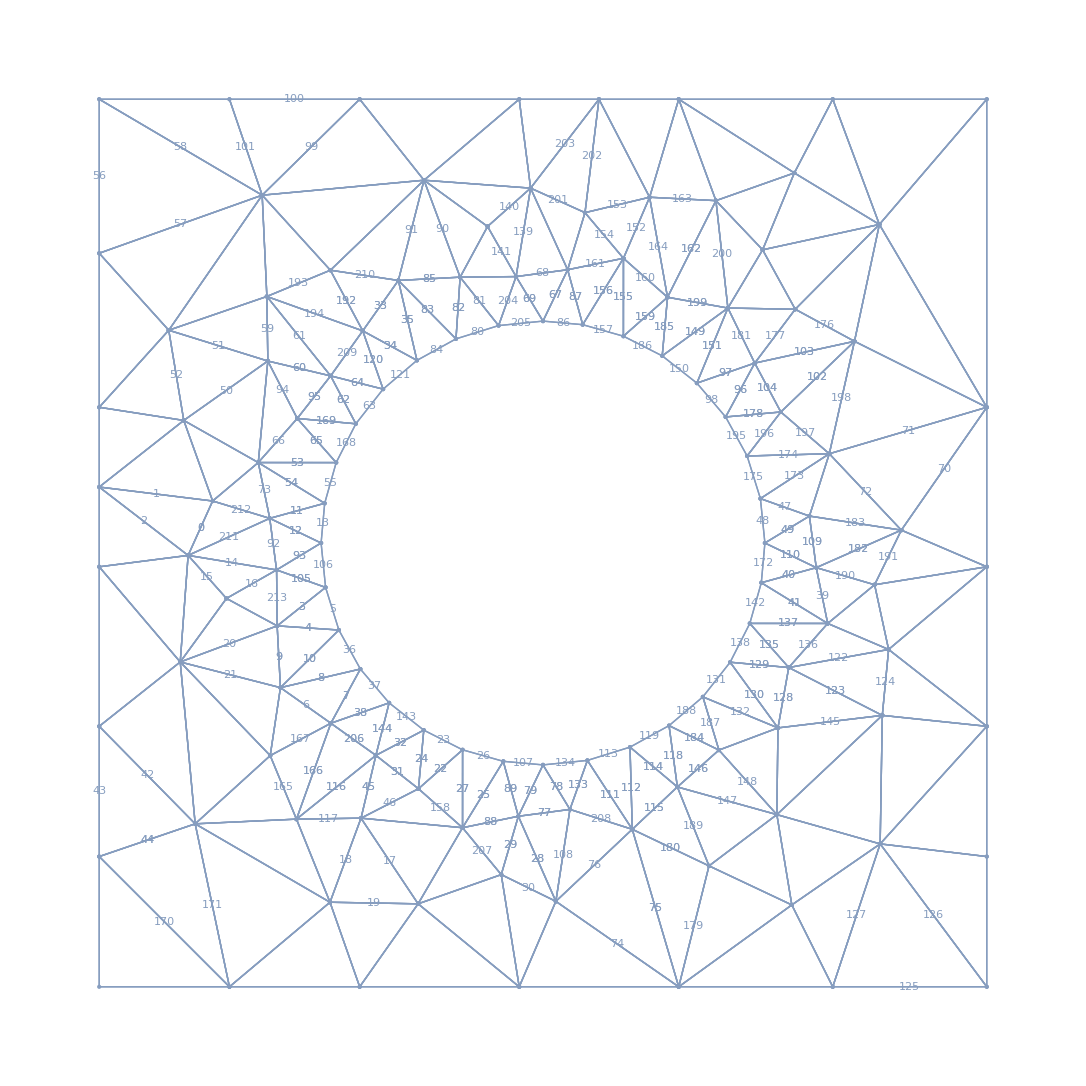

```mathematica
Show@𝒯
```